```mathematica
(*  Read the file as pairs of values (x,y) *)
(*  One day I will figure out how to say HERE *)
```

```mathematica
xy = ReadList [ "/Users/jburkardt/public_html/math_src/graphics_examples/scatter_plot.txt", {Number,Number} ]
```

{{0.641485,0.460798},{0.21224,0.616423},{0.297265,0.469856},{0.488776,0.725111},{0.339105,0.471877},{0.45764,0.549179},{0.40952,0.532359},{0.585937,0.37168},{0.706226,0.584342},{0.383187,0.325068},{0.480032,0.402636},{0.336109,0.777916},{0.605576,0.354974},{0.480064,0.448565},{0.707903,0.353563},{0.50494,0.660455},{0.385264,0.456237},{0.0782953,0.520131},{0.223198,0.428777},{0.556262,0.630618},{0.698637,0.29541},{0.600999,0.363691},{0.585965,0.513267},{0.591728,0.500687},{0.564319,0.417097},{0.558926,0.592664},{0.51225,0.549688},{0.705416,0.497237},{0.329245,0.696095},{0.706674,0.433156},{0.477103,0.513308},{0.716567,0.764645},{0.309706,0.317757},{0.520506,0.654578},{0.469266,0.511479},{0.421869,0.495565},{0.541647,0.355662},{0.320006,0.545032},{0.535131,0.413055},{0.546373,0.157184},{0.558404,0.481309},{0.604616,0.358846},{0.569051,0.325596},{0.438625,0.499356},{0.532102,0.756018},{0.548747,0.556879},{0.452534,0.173994},{0.599018,0.559104},{0.479271,0.726865},{0.430213,0.478743},{0.306031,0.590481},{0.413956,0.592264},{0.31089,0.538083},{0.727323,0.35791},{0.592872,0.42249},{0.319056,0.331467},{0.524164,0.737951},{0.510815,0.697311},{0.441361,0.307213},{0.357976,0.232611},{0.280266,0.145777},{0.66452,0.477828},{0.218469,0.425885},{0.472134,0.128344},{0.478993,0.68348},{0.634561,0.193336},{0.41702,0.520386},{0.5594,0.433029},{0.680798,0.508752},{0.735891,0.754064},{0.211893,0.565577},{0.534696,0.419912},{0.474753,0.46012},{0.478905,0.504368},{0.450586,0.465039},{0.644443,0.620655},{0.483039,0.68042},{0.70749,0.369799},{0.397839,0.583334},{0.466188,0.646366},{0.479089,0.678168},{0.683332,0.438668},{0.494813,0.365794},{0.591315,0.603347},{0.468364,0.467194},{0.363701,0.545071},{0.661215,0.421198},{0.280257,0.612411},{0.279553,0.550493},{0.555237,0.571764},{0.273012,0.539687},{0.405671,0.398654},{0.500652,0.516245},{0.691681,0.636216},{0.617951,0.47593},{0.246928,0.178976},{0.793118,0.461888},{0.533235,0.611309},{0.397624,0.328304},{0.48862,0.591612},{0.749057,0.7549},{0.376466,0.415258},{0.337731,0.50547},{0.519279,0.631932},{0.486366,0.41816},{0.800571,0.619546},{0.47772,0.715695},{0.550127,0.700517},{0.546518,0.311481},{0.621581,0.545679},{0.67178,0.357132},{0.386017,0.61925},{0.431451,0.563907},{0.61639,0.521601},{0.424679,0.607041},{0.614539,0.35066},{0.579578,0.197863},{0.619489,0.462663},{0.718761,0.332019},{0.440508,0.57854},{0.618579,0.413813},{0.590221,0.487848},{0.718087,0.634694},{0.30366,0.626914},{0.442461,0.551107},{0.637876,0.48424},{0.511571,0.561545},{0.662909,0.609976},{0.540175,0.497741},{0.182839,0.838856},{0.517329,0.363428},{0.551044,0.555589},{0.623494,0.407383},{0.465886,0.528396},{0.695534,0.274515},{0.337148,0.230229},{0.339199,0.747778},{0.421933,0.632252},{0.440489,0.408304},{0.43814,0.502178},{0.385785,0.657791},{0.35756,0.547289},{0.569223,0.527477},{0.370498,0.49542},{0.696909,0.625154},{0.638647,0.45298},{0.146411,0.520268},{0.442068,0.47726},{0.44025,0.422353},{0.253925,0.281638},{0.446131,0.317128},{0.6674,0.660569},{0.491226,0.610534},{0.435959,0.455795},{0.467128,0.547975},{0.437234,0.441017},{0.503828,0.528979},{0.307917,0.737752},{0.520273,0.865401},{0.718018,0.64212},{0.70693,0.218408},{0.550159,0.39764},{0.517011,0.570555},{0.433709,0.48645},{0.204664,0.585956},{0.680902,0.71039},{0.332427,0.487278},{0.730759,0.625588},{0.448003,0.575663},{0.363451,0.610571},{0.487175,0.575924},{0.698802,0.703893},{0.585431,0.671102},{0.54122,0.332623},{0.711524,0.633809},{0.360473,0.795202},{0.53644,0.304696},{0.636691,0.331823},{0.312566,0.72731},{0.405785,0.248865},{0.490541,0.311421},{0.408753,0.429301},{0.676186,0.657849},{0.683514,0.456843},{0.61463,0.408758},{0.631355,0.276021},{0.723431,0.240494},{0.598947,0.684105},{0.639804,0.541591},{0.806676,0.532626},{0.344093,0.614842},{0.507829,0.750655},{0.572202,0.655199},{0.486688,0.471466},{0.281495,0.589602},{0.530464,0.374917},{0.520181,0.571423},{0.43622,0.743018},{0.426429,0.728349},{0.664057,0.852507},{0.775938,0.5222},{0.518592,0.706812},{0.538094,0.318744},{0.519066,0.401149},{0.616518,0.282051},{0.521087,0.489348},{0.666576,0.427829},{0.563633,0.662687},{0.598167,0.484063},{0.724189,0.584813},{0.672886,0.52124},{0.590517,0.659232},{0.576889,0.662347},{0.399916,0.528245},{0.377996,0.447248},{0.537154,0.473287},{0.37262,0.235317},{0.631744,0.493869},{0.276705,0.807678},{0.58491,0.536429},{0.495758,0.551739},{0.464044,0.356256},{0.502878,0.343306},{0.105173,0.659629},{0.570042,0.347611},{0.588855,0.38321},{0.559337,0.290846},{0.609004,0.533558},{0.682013,0.424862},{0.54217,0.385011},{0.588378,0.511276},{0.526199,0.569923},{0.185898,0.46146},{0.498205,0.441891},{0.383644,0.585753},{0.53884,0.2105},{0.561262,0.41648},{0.532186,0.458422},{0.58586,0.435985},{0.198207,0.550299},{0.435454,0.351942},{0.516876,0.543626},{0.522306,0.584065},{0.384222,0.662969},{0.369018,0.342973},{0.138014,0.697602},{0.371458,0.526786},{0.561545,0.511874},{0.22996,0.844369},{0.753108,0.531907},{0.469434,0.486173},{0.565164,0.350545},{0.266964,0.552146},{0.486405,0.257693},{0.445375,0.635276},{0.571544,0.555419},{0.380342,0.438332},{0.390817,0.379978},{0.248921,0.531082},{0.410622,0.341223},{0.603948,0.499318},{0.670242,0.319189},{0.218133,0.279184},{0.58762,0.399259},{0.576192,0.548754},{0.626339,0.530895},{0.649149,0.214059},{0.376189,0.446564},{0.495641,0.648754},{0.617987,0.399244},{0.441692,0.577176},{0.355931,0.514292},{0.303475,0.654702},{0.377199,0.623842},{0.398189,0.52293},{0.414058,0.314334},{0.477625,0.446991},{0.503897,0.227204},{0.391107,0.536803},{0.755753,0.321909},{0.482206,0.800079},{0.562321,0.288394},{0.506021,0.366649},{0.423924,0.461837},{0.583914,0.379757},{0.292746,0.149227},{0.42053,0.448103},{0.703224,0.581107},{0.470362,0.381528},{0.454012,0.511447},{0.531272,0.537092},{0.719123,0.511081},{0.587981,0.351097},{0.550373,0.377732},{0.598401,0.616034},{0.531195,0.638125},{0.763095,0.629258},{0.382684,0.815068},{0.569248,0.575928},{0.39352,0.648311},{0.632327,0.291257},{0.414439,0.39935},{0.415875,0.550501},{0.386525,0.299907},{0.627676,0.552689},{0.522062,0.470536},{0.547652,0.347385},{0.256623,0.154154},{0.489993,0.514604},{0.568782,0.572924},{0.423341,0.308053},{0.543034,0.385142},{0.289292,0.428317},{0.737566,0.340372},{0.393018,0.398668},{0.523382,0.779122},{0.628491,0.332405},{0.489714,0.696611},{0.54133,0.513125},{0.453219,0.621759},{0.464017,0.184179},{0.700014,0.300715},{0.481994,0.43332},{0.378338,0.30977},{0.347917,0.297986},{0.643847,0.535787},{0.718142,0.554443},{0.298151,0.530158},{0.627949,0.398953},{0.403013,0.393632},{0.650393,0.470514},{0.662217,0.68597},{0.277686,0.470752},{0.528765,0.451136},{0.430752,0.315283},{0.419766,0.420908},{0.323371,0.544169},{0.623345,0.275624},{0.297984,0.532476},{0.261205,0.688814},{0.618015,0.496631},{0.540992,0.441077},{0.491392,0.403194},{0.685297,0.624292},{0.432684,0.534989},{0.746492,0.485136},{0.346869,0.513211},{0.475455,0.71869},{0.32623,0.416776},{0.488717,0.621645},{0.272904,0.72119},{0.332698,0.240717},{0.346251,0.493866},{0.346342,0.450198},{0.7636,0.57677},{0.29302,0.474565},{0.447221,0.558994},{0.566662,0.556059},{0.579001,0.623651},{0.624576,0.430684},{0.527436,0.423625},{0.388121,0.474255},{0.410923,0.491945},{0.428452,0.276293},{0.479255,0.603876},{0.723288,0.685528},{0.180834,0.693682},{0.470602,0.664644},{0.478819,0.466755},{0.538388,0.691042},{0.57425,0.410783},{0.401579,0.466752},{0.440988,0.326981},{0.428017,0.641477},{0.51999,0.321946},{0.535628,0.451999},{0.531758,0.161572},{0.555489,0.548209},{0.430839,0.48764},{0.29652,0.413166},{0.519339,0.479291},{0.577917,0.423637},{0.726154,0.39096},{0.605056,0.569743},{0.526129,0.630466},{0.355899,0.428613},{0.477067,0.300094},{0.58985,0.530474},{0.497758,0.483634},{0.34543,0.544273},{0.439641,0.467962},{0.441727,0.728586},{0.449485,0.374576},{0.448301,0.725973},{0.390656,0.51901},{0.482977,0.335247},{0.677778,0.275053},{0.265766,0.478753},{0.187603,0.38976},{0.555958,0.626228},{0.343946,0.559843},{0.733853,0.523689},{0.230474,0.554079},{0.587707,0.636934},{0.422792,0.678151},{0.366572,0.918555},{0.440567,0.382759},{0.65764,0.360532},{0.567201,0.70262},{0.244027,0.872784},{0.342917,0.352698},{0.198355,0.659456},{0.392516,0.422006},{0.566715,0.574837},{0.367719,0.371142},{0.39233,0.605767},{0.346116,0.589367},{0.499917,0.615756},{0.648316,0.456902},{0.503859,0.51546},{0.399241,0.549176},{0.51069,0.353198},{0.562628,0.728581},{0.36897,0.76886},{0.561024,0.542859},{0.609899,0.505469},{0.612277,0.522479},{0.23603,0.608227},{0.483926,0.34718},{0.669213,0.438311},{0.5425,0.297394},{0.610668,0.412872},{0.463326,0.554591},{0.691641,0.422216},{0.427509,0.672858},{0.672194,0.306692},{0.384675,0.352751},{0.580933,0.660183},{0.336874,0.296768},{0.525722,0.473182},{0.401566,0.648351},{0.281806,0.521646},{0.584263,0.428197},{0.525562,0.442395},{0.337125,0.372131},{0.531312,0.376544},{0.627165,0.508837},{0.513421,0.377292},{0.24474,0.619598},{0.536449,0.474382},{0.392516,0.431172},{0.474862,0.36496},{0.576262,0.521549},{0.660454,0.686166},{0.602105,0.774198},{0.295848,0.474715},{0.657134,0.501077},{0.672545,0.568511},{0.586951,0.450907},{0.561496,0.589983},{0.525678,0.495876},{0.422251,0.374632},{0.53876,0.454606},{0.387153,0.577031},{0.309168,0.614091},{0.581521,0.77195},{0.624539,0.333718},{0.429299,0.425842},{0.854699,0.381067},{0.434656,0.762434},{0.475502,0.639234},{0.838309,0.636501},{0.22582,0.528003},{0.400785,0.534309},{0.333852,0.594612},{0.635497,0.520496},{0.631887,0.658466},{0.397329,0.376523},{0.591563,0.550303},{0.448148,0.472488},{0.442419,0.774717},{0.251104,0.558179},{0.800725,0.334315},{0.316523,0.601158},{0.696458,0.763285},{0.183475,0.511001},{0.624615,0.555368},{0.56793,0.387822},{0.351092,0.442796},{0.374924,0.537282},{0.44675,0.296666},{0.493666,0.45568},{0.792114,0.422022},{0.591118,0.639375},{0.62021,0.567402},{0.340843,0.278966},{0.684589,0.526018},{0.526641,0.488727},{0.578012,0.72232},{0.588328,0.577763}}

```mathematica
(*  Create the image *)
```

```mathematica
g1 = ListPlot [ xy, PlotStyle->PointSize[0.02], DisplayFunction->Identity, PlotLabel->"Scatter Plot",
FrameLabel->{"<--- X --->","<--- Y --->"},Frame->{True,True,True,True},GridLines->{Automatic,Automatic},PlotRange->{{0.0,1.0},{0.0,1.0}}];
```

```mathematica
(* Display the image *)
```

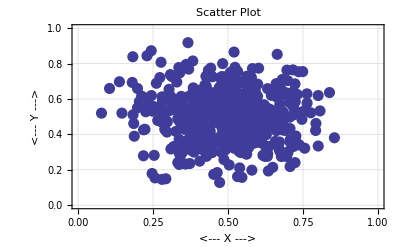

```mathematica
Show [ g1 ]
```

```mathematica
(* Export the image. *)
(* I have to say HERE using a huge string *)
```

```mathematica
Export["/Users/jburkardt/public_html/math_src/graphics_examples/scatter_plot.png", g1, "PNG" ]
```

/Users/jburkardt/public_html/math_src/graphics_examples/scatter_plot.png